f[x,y] — 将函数自变量放入方括号中
Exppaclet:ref/Exp, Dopaclet:ref/Do, ... — 以大写字母开头的内置符号
{…}paclet:ref/List (Listpaclet:ref/List)  ▪  "…"paclet:ref/String (Stringpaclet:ref/String)  ▪  e[[paclet:ref/Parti]]paclet:ref/Part (Partpaclet:ref/Part)  ▪  e[[i;;paclet:ref/Spanj]] (Spanpaclet:ref/Span)
x_paclet:ref/Blank — 模式，任意表达式(“x 空格”)
x__paclet:ref/BlankSequence, x___paclet:ref/BlankNullSequence — 任意表达式序列 (“x 双空格”， ……)
sym:obj 或 Patternpaclet:ref/Pattern[sym,obj] , 表示赋予名称 sym 的模式对象 obj.

@  Prefixpaclet:ref/Prefix[f[expr]] 以缺省形式 f@expr 输出给定的 f[expr].
Mappaclet:ref/Map (/@paclet:ref/Map) — 作用于列表： f/@{x,y,z}⟶{f[x],f[y],f[z]}/@ Map
Applypaclet:ref/Apply (@@paclet:ref/Apply) — 应用于一个列表： f@@{x,y,z}⟶f[x,y,z]
MapApplypaclet:ref/MapApply (@@@paclet:ref/MapApply) — 应用于一个列表： f@@@{x,y,z}⟶{f@@x,f@@y,f@@z}

/@paclet:ref/Map (Mappaclet:ref/Map — “slash at”)  ▪  @@paclet:ref/Apply(Applypaclet:ref/Apply)  ▪  @@@paclet:ref/MapApply (MapApplypaclet:ref/MapApply)  ▪  //=paclet:ref/Map (ApplyTopaclet:ref/ApplyTo)  ▪  ===paclet:ref/SameQ (SameQpaclet:ref/SameQ)

f[x,y] | f[x,y] 的标准形式
f@x | f[x] 的前缀形式,f@x+y 等于 f[x]+y 
x//f | f[x] 的后缀形式, x+y//f 等于 f[x+y] 
x~f~y | f[x,y] 的中缀形式

<< filepaclet:ref/Get — 输入文件 (>>paclet:ref/Putfile，>>>paclet:ref/PutAppendfile 用来输出一个文件) 
(* … *) — 注释
%paclet:ref/Out — 最近的输出 (%paclet:ref/Outn 为第 n 行的输出)

FoldList[f,x,{a,b,c}]   给出 {x,f[x,a],f[f[x,a],b],f[f[f[x,a],b],c]}
Through[{f,g,h}[x]]  给出 {f[x],g[x],h[x]}
Composition[f,g,h][x,y] 给出 f[g[h[x,y]]]
MapIndexed[f][{a,b,c,d}] 给出 {f[a,{1}],f[b,{2}],f[c,{3}],f[d,{4}]}
MapThread[f,{{a,b,c},{x,y,z}}] 给出 {f[a,x],f[b,y],f[c,z]}
Thread[f[{a,b,c},x]] 逐项作用， 给出  {f[a,x],f[b,x],f[c,x]}

expr/.rules 或 ReplaceAllpaclet:ref/ReplaceAll[expr,rules], 使用规则替代
RuleDelayed (:>, :>)(规则延迟)
p.. 或 Repeatedpaclet:ref/Repeated[p]
 是一个模式对象，表示一个或多个表达式的序列，每个表达式匹配 p. 
s_1~~s_2~~… 或 StringExpressionpaclet:ref/StringExpression[s_1,s_2,…]
表示字符串和符号字符串对象 s_i 组成的一个序列.
"s_1"<>"s_2"<>…，StringJoinpaclet:ref/StringJoin["s_1","s_2",…] 或 StringJoinpaclet:ref/StringJoin[{"s_1","s_2",…}]
Associationpaclet:ref/Association[key_1→val_1,key_2→val_2,…] 或 <|key_1→val_1,key_2→val_2,…|> 
表示键和值之间的关联.
body&paclet:ref/Function, x|->bodypaclet:ref/Function, x↦bodypaclet:ref/Function — 纯函数, 例如： (#+1)&
#paclet:ref/Slot,#2, ##paclet:ref/SlotSequence,##2, #namepaclet:ref/Slot — 纯函数中变量的插符
..paclet:ref/Repeated (Repeatedpaclet:ref/Repeated)  ▪  |paclet:ref/Alternatives (Alternativespaclet:ref/Alternatives)  ▪  /;paclet:ref/Condition (Conditionpaclet:ref/Condition)  ▪  ?paclet:ref/PatternTest (PatternTestpaclet:ref/PatternTest)

Outerpaclet:ref/Outer[f,list_1,list_2] | 广义外积
Innerpaclet:ref/Inner[f,list_1,list_2,g] | 广义内积

帮助 guide/Syntax  ref/Pattern  guide/NumberTheoreticFunctions

```mathematica
Prime@3
```

5

```mathematica
n=9!;FactorInteger[n]
Power@@@FactorInteger[n]
```

{{2,7},{3,4},{5,1},{7,1}}

{128,81,5,7}

```mathematica
BaseForm[5,2]
```

101_2

```mathematica
PowersRepresentations[2293,2,2]
PowersRepresentations[1729,2,3]
```

{{23,42}}

{{1,12},{9,10}}

expr/.rules或ReplaceAllpaclet:ref/ReplaceAll[expr,rules]

```mathematica
{x,x^2,y,z}/.x->{a,b}
```

{{a,b},{a^2,b^2},y,z}

```mathematica
s="Tally[list] lists distinct elements in the order they appear in list.";
Tally[Characters[s]]
```

{{T,1},{a,3},{l,6},{y,2},{[,1},{i,7},{s,6},{t,8},{],1},{ ,10},{d,2},{n,4},{c,1},{e,7},{m,1},{h,2},{o,1},{r,3},{p,2},{.,1}}

```mathematica
Characters[s]
InputForm[%]
StringJoin[%]
```

{T,a,l,l,y,[,l,i,s,t,], ,l,i,s,t,s, ,d,i,s,t,i,n,c,t, ,e,l,e,m,e,n,t,s, ,i,n, ,t,h,e, ,o,r,d,e,r, ,t,h,e,y, ,a,p,p,e,a,r, ,i,n, ,l,i,s,t,.}

Tally[list] lists distinct elements in the order they appear in list.

{"T", "a", "l", "l", "y", "[", "l", "i", "s", "t", "]", " ", "l", "i", "s", 
 "t", "s", " ", "d", "i", "s", "t", "i", "n", "c", "t", " ", "e", "l", "e", 
 "m", "e", "n", "t", "s", " ", "i", "n", " ", "t", "h", "e", " ", "o", "r", 
 "d", "e", "r", " ", "t", "h", "e", "y", " ", "a", "p", "p", "e", "a", "r", 
 " ", "i", "n", " ", "l", "i", "s", "t", "."}

```mathematica
WordData[]
Export["WordData.txt",WordData[]]
```

WordData.txt

```mathematica
WordData[All,"Verb"]
```

GatherBypaclet:ref/GatherBy[list,f] 
当应用 f，将 list 中每个集合中给出相同值的元素收集到子列表中.
GatherBypaclet:ref/GatherBy[list,{f_1,f_2,…}]
在层 i 应用 f_i 后，将 list 收集到嵌套列表中.

```mathematica
Tuples[{{a,b},{1,2},{x,y}}]
GatherBy[%,{First,Last}]
Map[Framed,%,{1,2}]
```

{{a,1,x},{a,1,y},{a,2,x},{a,2,y},{b,1,x},{b,1,y},{b,2,x},{b,2,y}}

{{{{a,1,x},{a,2,x}},{{a,1,y},{a,2,y}}},{{{b,1,x},{b,2,x}},{{b,1,y},{b,2,y}}}}

{{{{a,1,x},{a,2,x}},{{a,1,y},{a,2,y}}},{{{b,1,x},{b,2,x}},{{b,1,y},{b,2,y}}}}

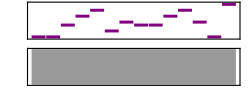

```mathematica
Sound[SoundNote/@Characters["CcEGADFEeGafCb"]]
```

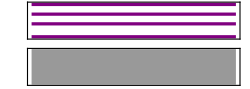

```mathematica
Sound[SoundNote[{"C","E","G","Bb"}]]
```

```mathematica
CountsBy[Range[1000],PrimeQ]
```

<|False→832,True→168|>

```mathematica
(*函数对 √3 进行牛顿逼近*)
newton3[x_]:=N[1/2 (x+3/x)]
NestList[newton3,1.0,5]
FixedPoint[newton3,1.0]
```

{1.,2.,1.75,1.73214,1.73205,1.73205}

1.73205

```mathematica
FoldList[f,x,{a,b,c}]
```

{x,f[x,a],f[f[x,a],b],f[f[f[x,a],b],c]}

```mathematica
Through[{f,g,h}[x]]
Through[(f+g+h)[x,y]]
```

{{},g[x],h[x]}

```mathematica
(*延迟规则，每次替换x时，增加n：*)
n=1;{x,x,a,b,x,x,c,d}/.x:>n++
```

{1,2,a,b,3,4,c,d}

```mathematica
Pi ∈ Reals
∈ <-> -> π
```

```mathematica
Array[g,5,0]
```

{g[0],g[1],g[2],g[3],g[4]}

```mathematica
?JuliaSetPlot
```

```mathematica
IntegerDigits[15,2,8]
```

{0,0,0,0,1,1,1,1}